```mathematica
*Q-1
```

```mathematica
Series[Exp[-x^4+x^3-x^2],{x,0,6}]
```

1-x^2+x^3-x^4/2-x^5+(4 x^6)/3+O[x]^7

```mathematica
*Q-2
```

```mathematica
Solve[x^4+3*x^3-3*x^2+10==0,x]
```

{{x→1-ⅈ},{x→1+ⅈ},{x→1/2 (-5-√5)},{x→1/2 (-5+√5)}}

```mathematica
*Q-3
```

```mathematica
f[x_]:=x^3*Log[x ]+Cosh[x]
```

```mathematica
f'''[x]
```

11+6 Log[x]+Sinh[x]

```mathematica
*Q-4
```

```mathematica
NIntegrate[Sqrt[1-x],{x,0,1}]
```

0.666667

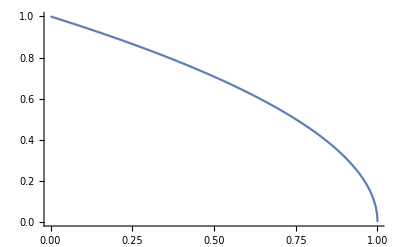

```mathematica
Plot[Sqrt[1-x],{x,0,1},PlotRange->All]
```

```mathematica
*Q-5
```

```mathematica
m={{1,2,3},{4,5,8},{3,2,1}}
```

{{1,2,3},{4,5,8},{3,2,1}}

```mathematica
MatrixForm[m]
```

(1 | 2 | 3
4 | 5 | 8
3 | 2 | 1)

```mathematica
im = Inverse[m]
```

{{-11/8,1/2,1/8},{5/2,-1,1/2},{-7/8,1/2,-3/8}}

```mathematica
MatrixForm[im]
```

(-11/8 | 1/2 | 1/8
5/2 | -1 | 1/2
-7/8 | 1/2 | -3/8)

```mathematica
*Q-6
```

```mathematica
s = NDSolve[{y''[t]==-1/4 π^2 (1+y[t]),y[0]==0,y[1]==1},y,{t,0,7}]
```

{{y→InterpolatingFunction[…]}}

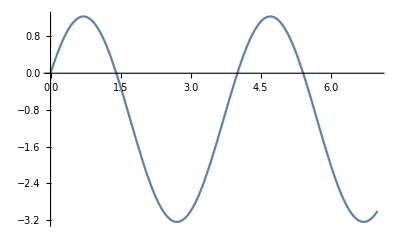

```mathematica
Plot[Evaluate[y[t]/.s],{t,0,7}]
```